# Propagazione di un’onda elastica in un materiale 2D a fori ripetuti

## Meccanica computazionale delle strutture 2

```mathematica
TextCell[
Grid[{{
TextCell["Docente:
Prof. Andrea Piccolroaz","Author", LineSpacing->{1}],
TextCell["Studente:
Matteo Franzoi - 216006", "Author", LineSpacing->{1}]
}},
Spacings->{40,0}],
"Author",
RGBColor["#214fa1"],
TextAlignment->Center
]//CellPrint
```

Docente:
Prof. Andrea Piccolroaz | Studente:
Matteo Franzoi - 216006

## Introduzione

```mathematica
L1 = L2 = 1;
H = L1/4;
n = 6;
plot1 = 
Show[
Graphics[
{ 
Black, Arrow[{{-L1, -L2}, {0, -L2}}], Arrow[{{-L1, -L2}, {-L1, 0}}],
Text[Style["e_1", Large], {0, -L2}, {Center, Top}],
Text[Style["e_2", Large], {-L1, 0}, {1.5, Center}]
}
],
Table[
{
Graphics[{
Gray,
Opacity[1],
Rectangle[{-L1/2,i*L2}, {(n-1/2)*L1+H,H+i*L2}],
Rectangle[{i*L1,-L2/2}, {i*L1+H,(n-1/2)*L2+H}]
}]
},
{i, 0,n-1}],
(* DIMENSIONS *)
Graphics[{
(* L1 *)
Text[Style["L_1", Large], {(L1+H)/2,(L2+H)/2}, {Center,Top}],
Black,
Arrowheads[{-.04,.04}], Arrow[{{H/2,(L2+H)/2}, {L1+H/2, (L2+H)/2}}],
(* L2 *)
Text[Style["L_2", Large], {(3L1+H)/2, (L2+H)/2}, {-1.5,0}],
Black,
Arrowheads[{-.04,.04}], Arrow[{{(3L1+H)/2, H/2}, {(3L1+H)/2, L2+H/2}}]
}],
(* DASHED RECTANGLE *)
Graphics[
{
EdgeForm[{Thick,Black,Dashed}], Opacity[0], Rectangle[{1/2*(3*L1+H), 1/2(3*L2+H)}, {1/2*(3*L1+H)+L1, 1/2(3*L2+H)+L2}]
}
],
ImageSize->800,
PlotRangePadding->{0,0}
];
(* -------------------------------------------------- *)
plot2 = 
Show[
Graphics[{
Gray,
Opacity[1],
Rectangle[{0,-H/2}, {L1, H/2}],
Rectangle[{(L1-H)/2, L2/2}, {(L1+H)/2, -L2/2}]
}]
,
Graphics[
{
(* L1 *)
Text[Style["L_1", Large], {L1/2,-(L2+H)/2}, {Center,Top}],
Black,
Arrowheads[{-.04,.04}], Arrow[{{0,-(L2+H)/2}, {L1, -(L2+H)/2}}],
(* L2 *)
Text[Style["L_2", Large], {L1+H/2, 0}, {-1.5,0}],
Black,
Arrowheads[{-.04,.04}], Arrow[{{(L1+H/2), -L2/2}, {(L1+H/2), L2/2}}],
(* H1 *)
Text[Style["H_1", Large], {L1/4, 0}, {1.5,0}],
Black,
Arrowheads[{-.04,.04}], Arrow[{{(L1/4), -H/2}, {(L1/4), H/2}}],
(* H2 *)
Text[Style["H_2", Large], {L1/2,-L2/4}, {Center,Top}],
Black,
Arrowheads[{-.04,.04}], Arrow[{{(L1-H)/2,-(L2)/4}, {(L1+H)/2, -(L2)/4}}]
}
],
Graphics[{Black, EdgeForm[Dashed], Opacity[0], Rectangle[{0,  -L2/2}, {L1, L2/2}]}],
ImageSize->800,
PlotRangePadding->{0,0}
];
(* ------------------- *)
GraphicsRow[{plot1,plot2}, Spacings->{100,0}, ImageSize->1000]
(*Grid[{{plot1, plot2}}, Spacings->{n,0}, Alignment->{Center}]*)
```

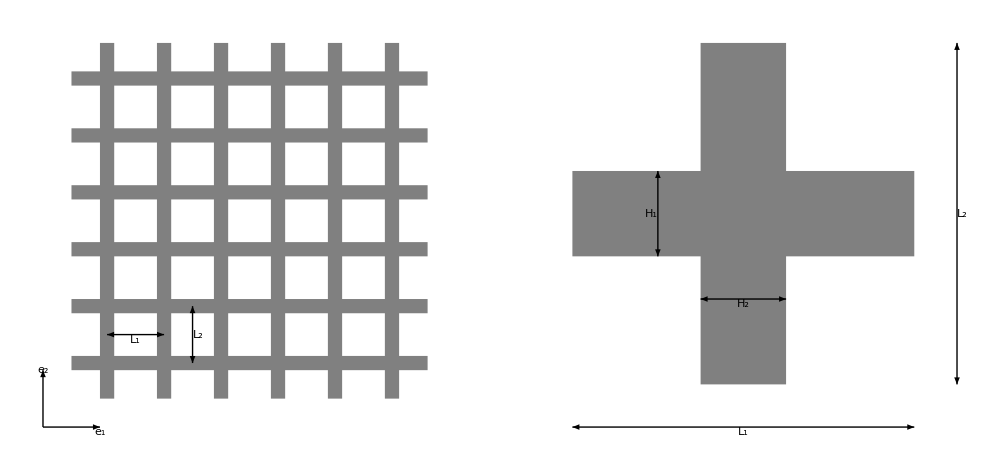
-Graphics-
A sinistra: reticolo di travi. A destra: rappresentazione della cella unitaria

Il problema della propagazione di onde elastiche in una struttura bidimensionale infinita a fori ripetuti (o metamateriale) è studiato da tempo e trova soluzioni in vari campi: dall’acustica fino all’ottica, dalla meccanica fino alla sismica. Esempi di applicazioni sono riportati da Bordiga et al., 20191 e mostrano come sia possibile, ad esempio, creare delle lenti piane attraverso l’applicazione di determinate condizioni al contorno.

Nel caso studio si analizzerà una geometria regolare composta da due orditure di travi ortogonali tra loro giacenti nel piano x_1 x_2 come mostrato nella figura sopra; considerata la forte simmetria in entrambe le direzioni è possibile analizzare la sola cella unitaria di dimensioni {L_1, H_1} e {L_2, H_2} rispettivamente per il tratto orizzontale (disposto lungo la direzione e_1) e per il tratto verticale (disposto lungo la direzione e_2); ripetendo la cella unitaria lungo le due direzioni principali si può facilmente ottenere il reticolo originale.

L’onda elastica si propagherà nel graticcio infinito generando deformazioni sia di tipo assiale che di tipo flessionale (nel piano); dato il regime di plain stress non sono presenti tensioni fuori piano.
La possibilità di considerare una qualsiasi cella unitaria è garantita dall’applicazione delle condizioni al contorno di Floquet-Bloch che consentono di definire matematicamente la periodicità del reticolo di travi. La formulazione matematica del teorema di Bloch verrà trattata nelle pagine successive.

Lo scopo è quello di studiare le superfici di dispersione delle onde nel metamateriale e di confontare il modello bidimensionale con dei modelli di trave le cui soluzioni sono note da G. Bordiga, L. Cabras, D. Bigoni, A. Piccolroaz, 20192.

Tutte le simulazioni sono state eseguite mediante il software agli elementi finiti COMSOL Multiphysics®.

```mathematica
CellPrint[TextCell["Teorema di Bloch", "Section", CellTags->"th_bloch"]]
```

## Teorema di Bloch

L’onda di Bloch è un’onda elastica piana modulata da una funzione periodica ϕ(x) caratterizzata dall’avere la medesima periodicità del mezzo in cui si propaga. Il teorema di Bloch è descritto dalla seguente relazione

```mathematica
MaTeX["
\\boldsymbol{u}(\\boldsymbol{x}) = \\boldsymbol{\\phi}(\\boldsymbol{x})\\,e^{i\\,\\boldsymbol{k}\\cdot\\boldsymbol{x}}
",Magnification->2.5]
```

-Graphics-

dove i=√-1 è l’unità immaginaria e k = { k_1, k_2}^T è il vettore di Bloch, le cui componeti sono k_i = (2π)/λ, con λ lunghezza d’onda; la funzione periodica deve perciò soddisfare la seguente condizione

```mathematica
MaTeX["
\\boldsymbol{\\phi} (\\boldsymbol{x} + \\boldsymbol{a}) = \\boldsymbol{\\phi}(\\boldsymbol{x})
",Magnification->2.5]
MaTeX[
"
\\forall \\, (\\boldsymbol{x}, \\boldsymbol{a}) \\in \\mathbb{R}^2
",Magnification->2.5
]
```

-Graphics-

-Graphics-

Come descritto da Bordiga et al., 20213 per un materiale periodico come in figura, con a_1 = {L_1, 0}^T e a_2 = {0,L_2}^T il teorema di Bloch si riduce a

```mathematica
MaTeX[
"\\boldsymbol{\\phi}(\\boldsymbol{x} + n_j \\boldsymbol{a}_j) = \\boldsymbol{\\phi}(\\boldsymbol{x} + n_1 \\boldsymbol{a}_1 + n_2\\boldsymbol{a}_2 )= \\boldsymbol{\\phi}(\\boldsymbol{x})",Magnification->2.5]
MaTeX["\\forall\\, (\\boldsymbol{x}, \\boldsymbol{a}_j) \\in\\mathbb{R}^2,~\\forall\\,n_j \\in \\mathbb{Z},~\\forall\\,j=1,2",Magnification->2.5]
```

-Graphics-

-Graphics-

La generica funzione u(x + n_j a_j) di un punto della cella unitaria si può facilmente ricavare come

```mathematica
MaTeX[
"
\\boldsymbol{u} (\\boldsymbol{x} + n_j\\,\\boldsymbol{a}_j) = \\boldsymbol{\\phi}(\\boldsymbol{x} + n_j \\boldsymbol{a}_j)\\, e^{i\\,\\boldsymbol{k}\\cdot (\\boldsymbol{x} +n_j\\,\\boldsymbol{a}_j) } = \\boldsymbol{\\phi}(\\boldsymbol{x})\\,e^{i\\,\\boldsymbol{k}\\cdot\\boldsymbol{x}}\\,e^{i\\,\\boldsymbol{k}\\cdot (n_j\\,\\boldsymbol{a}_j)} = \\boldsymbol{u} (\\boldsymbol{x}) \\, e^{i\\,\\boldsymbol{k}\\cdot (n_j\\,\\boldsymbol{a}_j)}
",Magnification->2.5
]
```

-Graphics-

A questo punto è sufficiente sostituire alla funzione u il vettore degli spostamenti nel piano, tale che u = {u, v}^T.

## Oggetto dello studio

Lo scopo dell’analisi è quello di ricavare le superfici di dispersione dell’onda elastica e quindi le frequenze proprie di vibrazione (o eigenfrequencies). Questo prevede oltre che una dipendenza dallo spazio data da k anche una dipendenza dal tempo. La soluzione generale del teorema di Bloch è del tipo

```mathematica
<<MaTeX`
MaTeX["
\\boldsymbol{u}(\\boldsymbol{x}, t) = \\boldsymbol{\\phi}(\\boldsymbol{x})\\,e^{i\\,\\boldsymbol{k}\\cdot \\boldsymbol{x}}\\,e^{-i\\,\\omega\\,t} = \\boldsymbol{\\phi}(\\boldsymbol{x})\\,e^{i (\\boldsymbol{k}\\cdot \\boldsymbol{x} - \\omega\\,t)}
", Magnification->2.5]

MaTeX["
\\boldsymbol{u} (\\boldsymbol{x} + n_j\\,\\boldsymbol{a}_j, t) = \\boldsymbol{u} (\\boldsymbol{x}) \\, e^{i (\\boldsymbol{k}\\cdot (n_j\\,\\boldsymbol{a}_j) - \\omega\\, t)}
", Magnification->2.5]

MaTeX["
\\boldsymbol{a}_j = \\{a_{j 1}, a_{j 2}\\}^T,\\quad j = 1,2
", Magnification->2.5]
```

-Graphics-

-Graphics-

-Graphics-

Applicando le condizioni di Floquet-Bloch si ottiene un sistema di equazioni lineari omogeneo (se non sono presenti forzanti) quale

```mathematica
<<MaTeX`
MaTeX["
\\boldsymbol{A}^\\star(\\omega, \\boldsymbol{k})\\,\\boldsymbol{q}^\\star = \\boldsymbol{0}
", Magnification->2.5]
```

-Graphics-

dove A^⋆(ω, k) = (Z(k))^H A(ω)Z(k),  q=Z(k)q^⋆ e con l’apice ^H che identifica l’operazione trasposta complessa coniugata.

Le frequenze angolari proprie ω sono la soluzione non banale del problema agli autovalori e dipenderanno implicitamente da k. Se il sistema è conservativo ci si aspetta che ω^2∈ ℝ.

Le superfici di dispersione di un’onda elastica rappresentano la relazione tra la frequenza e il numero d’onda dell’onda elastica in un materiale. Esse sono utilizzate per studiare le proprietà di propagazione dell’onda nel mezzo, quale ad esempio la velocità di propagazione, al variare delle caratteristiche geometriche e meccaniche del materiale.
Se l’onda si propaga lungo una sola direzione la relazione è una curva descritta dalla funzione ω=ω(k). Nel caso in esame, invece, le direzioni di propagazione dell’onda sono due: ciò implica una superficie tridimensionale nello spazio ω-k_1-k_2.

Dalla relazione di dispersione si possono definire due diverse velocità relative all’onda:

velocità di fase (o phase velocity), riferita alla velocità con cui la fase di un’onda (di lunghezza d’onda fissata) si propaga in un mezzo, è definita matematicamente come

```mathematica
<<MaTeX`
MaTeX["
v_{p,i} = \\frac{\\omega(\\boldsymbol{k})}{k_i}
", Magnification->2.5]
```

-Graphics-

velocità di gruppo (o group velocity), cioè la velocità con cui si propaga l’energia di un pacchetto d’onde (gruppo di onde con lunghezze d’onda differenti) in un mezzo, è descritta dal gradiente della superficie di dispersione

```mathematica
<< MaTeX`
MaTeX["
v_{g,i} = \\frac{\\partial\\omega(\\boldsymbol{k})}{\\partial k_i}
", Magnification -> 2.5]
```

-Graphics-

## Onde dispersive, non dispersive e stazionarie

Esistono diverse tipologie di onde - in base alla relazione tra ω e k: onde  dispersive, onde non dispersive e onde stazionarie (caso particolare di onde dispersive).

### Onde dispersive

Un’onda è dispersiva quando la relazione tra ω e k è non lineare. Per onde dispersive si ha v_g ≠ v_p come mostrato sotto: le velocità di fase e di gruppo sono rappresentate dalle pendenze delle rette magenta e rossa rispettivamente.

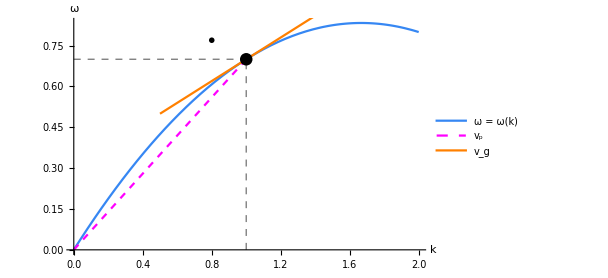
-Graphics- | -Graphics-
-Graphics-
-Graphics-

```mathematica
<<MaTeX`
Clear[a, b, c, d, f, k, k0]
f:=a*k-b*k^2 ;
k0=1;
a=1;
b=.3;
c = c/.Solve[c*k ==f/.k-> k0, c][[1]];
d = D[f, k]/.k->k0;
fig01 =Show[
Plot[ f, {k, 0, 2}, AxesLabel->{k, ω}, AxesStyle->FontSize->16, PlotLegends->{"ω = ω(k)"}],
Plot[c*k,{k, 0, k0}, PlotStyle->{Magenta, Dashed}, PlotLegends->{"v_p"}],
Plot[d*(k-k0)+c*k0, {k, .5,1.5}, PlotStyle->{Orange}, PlotLegends->{"v_g"}],
Graphics[{Dashed, Gray, Line[{{k0,0}, {k0,f/.k->k0}}] }],
Graphics[{Dashed, Gray, Line[{{0,f/.k->k0}, {k0,f/.k->k0}}] }],
Graphics[{Black, PointSize[.02], Point[{1,c}] }],
Graphics[{Text[MaTeX["\\{k_0, \\omega_0\\}", Magnification->2], {.8k0, 1.1c*k0}]}],
 ImageSize->450];

text01 =MaTeX["
\\omega = a\\, k - b\\, k^2,\\quad \\{a,b\\}=const > 0
",Magnification->2.5];

text02 = MaTeX["
v_p = \\frac{\\omega}{k}\\Big|_{k=k_0} = \\frac{\\omega_0}{k_0} = a - b\\, k_0
",Magnification->2.5];

text03=MaTeX["
v_g = \\frac{d \\omega}{d k}\\Big|_{k=k_0} = a - 2 b\\,k_0 < v_p
",Magnification->2.5];

TableForm[{{fig01, {text01, text02, text03}}}, TableSpacing->{2, 10, 3}]
```

Come si può notare dalla figura sopra, a basse frequenze la relazione è pressoché lineare (non dispersiva) mentre all’aumentare della frequenza questa si discosta dalla retta generando dispersione. Se v_g< v_p il pacchetto d’onde (wave packet) si muove con velocità inferiore alle onde che lo compongono.

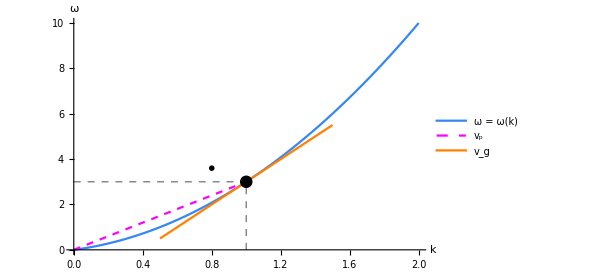
-Graphics- | -Graphics-
-Graphics-
-Graphics-

```mathematica
<<MaTeX`
Clear[a, b, c, d, f, k, k0]
f:=a*k+b*k^2 ;
k0=1;
a=1;
b=2;
c = c/.Solve[c*k ==f/.k-> k0, c][[1]];
d = D[f, k]/.k->k0;
fig01 =Show[
Plot[ f, {k, 0, 2}, AxesLabel->{k, ω}, AxesStyle->FontSize->16, PlotLegends->{"ω = ω(k)"}],
Plot[c*k,{k, 0, k0}, PlotStyle->{Magenta, Dashed}, PlotLegends->{"v_p"}],
Plot[d*(k-k0)+c*k0, {k, .5,1.5}, PlotStyle->{Orange}, PlotLegends->{"v_g"}],
Graphics[{Dashed, Gray, Line[{{k0,0}, {k0,f/.k->k0}}] }],
Graphics[{Dashed, Gray, Line[{{0,f/.k->k0}, {k0,f/.k->k0}}] }],
Graphics[{Black, PointSize[.02], Point[{1,c}] }],
Graphics[{Text[MaTeX["\\{k_0, \\omega_0\\}", Magnification->2], {.8k0, 1.2c*k0}]}],
 ImageSize->450];

text01 =MaTeX["
\\omega = a\\, k + b\\, k^2,\\quad \\{a,b\\}=const > 0
",Magnification->2.5];

text02 = MaTeX["
v_p = \\frac{\\omega}{k}\\Big|_{k=k_0} = \\frac{\\omega_0}{k_0} = a + b\\, k_0
",Magnification->2.5];

text03=MaTeX["
v_g = \\frac{d \\omega}{d k}\\Big|_{k=k_0} = a + 2 b\\,k_0 > v_p
",Magnification->2.5];

TableForm[{{fig01, {text01, text02, text03}}}, TableSpacing->{2, 10, 3}]
```

Al contrario, se v_g > v_p il wave packet si muove con velocità maggiore delle onde che lo compongono.

### Onde non dispersive

Si parla di onde non dispersive quando ω è proporzionale a k, o meglio quando la velocità di fase v_p è indipendente da k; tutte le onde viaggiano alla stessa velocità poiché la velocità del wave packet è uguale alla velocità dell’onda (v_g=v_p)

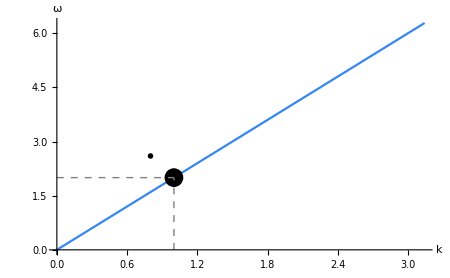
-Graphics- | -Graphics-
-Graphics-
-Graphics-

```mathematica
<<MaTeX`
Clear[f, c, k];
c=2;
f:=c*k;
k0=1;

fig01 =Show[
Plot[f, {k, 0, Pi}, AxesLabel->{k, ω}, AxesStyle->FontSize->16],
Graphics[{Black, PointSize[.03], Point[{k0, f/.k->k0}]}],
Graphics[{Black, Text[MaTeX["\\{k_0, \\omega_0\\}", Magnification->2], {.8*k0, 1.3*f/.k->k0}]}],
Graphics[{Dashed, Gray, Line[{{k0,0}, {k0,f/.k->k0}}] }],
Graphics[{Dashed, Gray, Line[{{0,f/.k->k0}, {k0,f/.k->k0}}] }],
 ImageSize->450];

text01 =MaTeX["
\\omega = c\\, k,\\quad c=const > 0
",Magnification->2.5];

text02 = MaTeX["
v_p = \\frac{\\omega}{k}\\Big|_{k=k_0} = c
",Magnification->2.5];

text03=MaTeX["
v_g = \\frac{d \\omega}{d k}\\Big|_{k=k_0} = c = v_p 
",Magnification->2.5];

TableForm[{{fig01, {text01, text02, text03}}}, TableSpacing->{2, 10, 3}]
```

### Onde stazionarie

Esiste la particolare condizione tale per cui la group velocity è nulla (v_g=0); in questo caso l’onda elastica è detta stazionaria: non c’è propagazione di energia attraverso il mezzo ma solo un’oscillazione nel tempo.

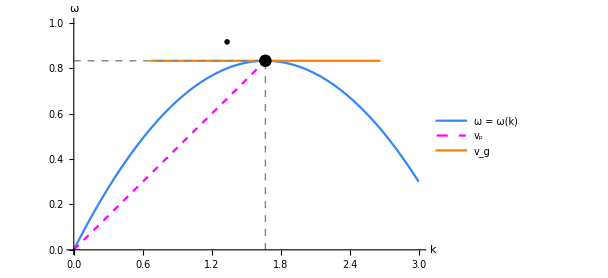
-Graphics- | -Graphics-
-Graphics-
-Graphics-

```mathematica
<<MaTeX`
Clear[a, b, c, d, f, k, k0]
f:=a*k-b*k^2 ;
a=1;
b=.3;
k0=k/.Solve[D[f,k]==0, k][[1]];
c = c/.Solve[c*k ==f/.k-> k0, c][[1]];
d = D[f, k]/.k->k0;

fig01 =Show[
Plot[ f, {k, 0, 3}, AxesLabel->{k, ω}, AxesStyle->FontSize->16, PlotLegends->{"ω = ω(k)"}, PlotRange->{{0,3}, {0, 1}}],
Plot[c*k,{k, 0, k0}, PlotStyle->{Magenta, Dashed}, PlotLegends->{"v_p"}],
Plot[d*(k-k0)+c*k0, {k, k0-1,k0+1}, PlotStyle->{Orange}, PlotLegends->{"v_g"}],
Graphics[{Dashed, Gray, Line[{{k0,0}, {k0,f/.k->k0}}] }],
Graphics[{Dashed, Gray, Line[{{0,f/.k->k0}, {k0,f/.k->k0}}] }],
Graphics[{Black, PointSize[.02], Point[{k0,f/.k->k0}] }],
Graphics[{Text[MaTeX["\\{k_0, \\omega_0\\}", Magnification->2], {.8k0, 1.1f/.k->k0}]}],
 ImageSize->450];

text01 =MaTeX["
\\omega = a\\, k - b\\, k^2,\\quad \\{a,b\\}=const > 0
",Magnification->2.5];

text02 = MaTeX["
v_p = \\frac{\\omega}{k}\\Big|_{k=k_0} = \\frac{\\omega_0}{k_0} = a - b\\, k_0
",Magnification->2.5];

text03=MaTeX["
v_g = \\frac{d \\omega}{d k}\\Big|_{k=k_0} = 0
",Magnification->2.5];

TableForm[{{fig01, {text01, text02, text03}}}, TableSpacing->{2, 10, 3}]
```

## Caratterizzazione del modello 2D in COMSOL Multiphysics®

### Caratteristiche geometriche e del materiale

COMSOL Multiphysics®, al contrario di altri software, considera le grandezze di input come dimensionali. Il modello è stato quindi creato tenendo conto della coerenza dimensionale tra i parametri, ma con valori del tutto arbitrari. Lunghezza, area e densità degli elementi sono state assunte come unitarie - in modo da generare una cella quadrata, altri parametri invece derivano dalla compatibilità dimensionale; i parametri principali sono:

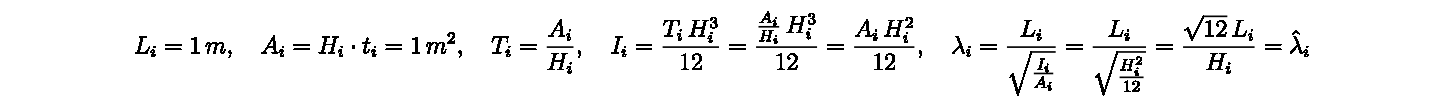

-Graphics-

```mathematica
MaTeX["
L_i = 1\\,m,\\quad A_i = H_i\\cdot t_i = 1\\,m^2,\\quad T_i = \\frac{A_i}{H_i},\\quad I_i = \\frac{T_i\\, H_i^3}{12} = \\frac{\\frac{A_i}{H_i}\\,H_i^3}{12} = \\frac{A_i\\,H_i^2}{12},\\quad \\lambda_i = \\frac{L_i}{\\sqrt{\\frac{I_i}{A_i}}} = \\frac{L_i}{\\sqrt{\\frac{H_i^2}{12}}} = \\frac{\\sqrt{12}\\,L_i}{H_i} = \\hat{\\lambda}_i
", Magnification->2.5]
MaTeX["
E_i = 1\\,\\frac{N}{m^2},\\quad G_i = \\frac{E_i}{2(1+\\nu_i)}, \\quad \\nu_i = 0,\\quad\\rho_i = 1\\,\\frac{kg}{m^3},
", Magnification->2.5]
```

con i = 1,2; L e H sono rispettivamente la lunghezza e lo spessore nel piano degli elementi, A è l’area della sezione trasversale, T è la profondità lungo la direzione z, I è il momento di inerzia attorno all’asse z, λ è la snellezza adimensionale e λ̂ è snellezza fissata; per quanto riguarda le caratteristiche del materiale: E è il modulo elastico, G è il modulo di taglio, ν  è il coefficiente di Poisson e ρ  è la densità per unità di volume.

Sono state considerate tre diversi valori di snellezza adimensionale: λ=10,  λ=20 e  λ=50. Come riportato in figura sotto gli spessori nel piano e la profondità fuori piano degli elementi sono influenzati dalla snellezza: all’aumentare di λ aumenta T e diminuisce H.

```mathematica
<<MaTeX`
Clear[fig1, λ];
fig1[λ_] =Module[{},
L1 = 1;
H1 =(√12)/λ;
T1 = 1/H1;
p0= {L1/2+H1/2, L1/2+H1/2, T1/2};
p1 = {H1/2,L1/2,0};
p2 = {L1/2, H1/2, 0};
v1 = {L1, 0, 0};
v2 = {0, H1, 0};
v3 = {0, 0, T1};
v4 = {H1,0,0};
v5 = {0, L1, 0};
v6 = {0,0,T1};
 Show[
Graphics3D[{
Opacity[0.5],
Parallelepiped[p1,{v1,v2,v3}]
}],
Graphics3D[{
Opacity[0.5],
Parallelepiped[p2,{v4,v5,v6}]
}],
(* x-axes *)
Graphics3D[{
Thick,
Arrowheads[.03], Arrow[{p0, p0 +1.2*{L1/2, 0, 0}}]
}],
Graphics3D[{Text[MaTeX["x",Magnification->2.5],p0+1.3*{L1/2,0,0}]}],
(* y-axes *)
Graphics3D[{
Thick,
Arrowheads[.03], Arrow[{p0, p0 +1.2*{0, L1/2, 0}}]
}],
Graphics3D[{Text[MaTeX["y",Magnification->2.5],p0+1.3*{0,L1/2,0}]}],
(* z-axis *)
Graphics3D[{
Thick,
Arrowheads[.03], Arrow[{p0, p0 -1.2*{0, 0, T1/2}}]
}],
Graphics3D[{Text[MaTeX["z",Magnification->2.5],p0-1.3*{0,0,T1/2}]}],
Boxed->False,
Axes->False,
AxesLabel->{x,y};
AxesOrigin->p0,
ViewVertical->{0, 0, 1},
PlotRangePadding->{{0,0},{0,0},{0,0}},
ImagePadding->{{0,0},{0,0}},
ImageSize->Large,
AspectRatio->{1,1,1},
PlotLabel->Text[Style[HoldForm["λ" = λ], FontSize->18]]
]
];
GraphicsRow[{fig1[10], fig1[20], fig1[50]}, Spacings->50, ImageSize->Large, ImagePadding->10]
```

-Graphics-

Variazione dei parametri geometrici al variare della snellezza

### Condizioni al contorno di Floquet-Bloch

Una volta definita la geometria del problema si passa all’applicazione delle condizioni al contorno. Come già detto, la particolare geometria del reticolo consente di studiare la cella unitaria a patto di applicare delle precise condizioni al contorno periodiche, dette anche condizioni di Floquet-Bloch. In COMSOL Multiphysics® sono presenti diverse condizioni di periodicità, tra cui quelle di Floquet che prevedono la definizione di una superficie sorgente (src) e una superficie di destinazione (dst) per ogni direzione di propagazione (nel caso in esame sia in direzione e_1 che in direzione e_2) e l’inserimento delle componenti del vettore di Bloch k_1, k_2 che verranno fatte variare durante l’analisi all’interno del loro dominio di definizione (k ∈ [0, π/L_1] × [0,π/L_2]).

-Graphics-	-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
A sinistra e in centro: definizione delle superfici sorgente e di destinazione per l’applicazione delle BCs di Floquet-Bloch. A destra: definizione del parametric sweep di k_1 e k_2

La variazione dei parametri k_i è stata fatta in COMSOL Multiphysics® tramite il cosiddetto parametric sweep, tenendo conto di tutte le possibili combinazioni dei due parametri, con n - numero di step da eseguire - fissato a 20.

### Impostazione della mesh

Sono state considerate varie mesh che verranno successivamente confrontate e infittite per verificare la convergenza della soluzione. Le mesh considerate sono costituite da:

EF triangolari (bi)quadratici a 6 nodi;

EF quadrangolari (bi)quadratici a 8 nodi con funzioni di forma di tipo serendipity;

EF quadrangolari (bi)quadratici a 9 nodi con funzioni di forma di Lagrange;

La dimensione massima di partenza dell’EF è stata scelta pari a 0.12m, per poi essere ridotta fino a 0.067m.

All’interno del tool Mesh di COMSOL Multiphysics® si può trovare una misura della qualità della mesh creata, basata su vari parametri tra cui skewness, maximum angle, growth rate, etc; la qualità è compresa tra 0 (zero - elemento degenerato) e 1 (qualità massima - EF equilateri/equiangolari). In generale COMSOL Multiphysics® consiglia di mantenere una qualità del EF al di sopra del valore  0.1.

-Graphics-               -Graphics-
A sinistra: qualità  EF triangolari. A destra: qualità  EF quadrangolari

-Graphics-          -Graphics-
A sinistra: qualità primo raffinamento. A destra: qualità secondo raffinamento

La qualità dell’EF secondo il criterio skewness risulta essere ben al di sopra del valore minimo consigliato dal software.

Di notevole importanza per le condizioni al contorno di Floquet-Bloch e quindi per la periodicità della soluzione è la disposizione degli elementi finiti sul contorno di “destinazione” che deve essere la stessa del contorno sorgente; è possibile farlo attraverso il comando copy, copiando tali e quali gli elementi finiti dal contorno in ingresso sul contorno in uscita.

Di seguito è riportata la tabella che riassume il numero di nodi e la qualità media degli EF secondo vari parametri, generata in automatico dal software.

"Comparazione dei valori medi di qualità delle mesh usate secondo COMSOL Multiphysics®"
"" | "Triangular coarse" | "Quad coarse" | "Triangular adapted 1" | "Triangular adapted 2"
"nodes num" | 90 | 36 | 1088 | 3729
"skewness" | 0.7919 | 0.9772 | 0.8934 | 0.8633
"max angle" | 0.8961 | 0.9772 | 0.9389 | 0.9203
"growth rate" | 0.7855 | 0.9591 | 0.8822 | 0.8545

## Superfici di dispersione

I risultati qui riportati derivano dallo studio delle frequenze proprie (eigenfrequencies) della cella unitaria precedentemente definita a cui sono state assegnate le stesse caratteristiche geometriche e meccaniche per gli elementi che la costituiscono (i.e. L_1=L_2=1m, A_1=A_2=1 m^2, ρ_1=ρ_2=1 kg/m^3, E_1=E_2=1Pa, etc).

-Graphics3D-
Prime sei superfici di dispersione relative alla snellezza adimensionale λ=20

La figura riporta le prime sei superfici di dispersione (riferite alle prime sei frequenze proprie al variare di k), la cui frequenza angolare ω è stata adimensionalizzata attraverso una frequenza di riferimento calcolata a partire dalla frequenza del primo modo assiale di una trave appoggio-appoggio di lunghezza L, modulo di elasticità E e densità ρ

```mathematica
<<MaTeX`
MaTeX[
"
\\omega^a_1 = \\frac{\\pi}{L}\\,\\sqrt{\\frac{E}{\\rho}}\\qquad \\Longrightarrow\\qquad \\omega_{ref} = \\frac{1}{L_1}\\,\\sqrt{\\frac{E}{\\rho}} = 1\\,s^{-1}
",
Magnification->2.5
]
```

-Graphics-

Le superfici sono ordinate dal basso verso l’alto seguendo i modi propri e non possono intersecarsi tra loro: ogni punto della superficie descrive il modo di propagazione dell’onda fissata la frequenza propria e il vettore d’onda e perciò la relazione di dispersione è unica per ogni set di valori {k_1,k_2,ω}. 
La prima superficie rappresenta il primo modo di vibrare, perciò non può esistere alcuna frequenza ω<ω_1 che descriva una superficie di dispersione. Ora si assuma, per assurdo, che le prime due superfici di dispersione si intersechino nel punto {(k̃)_1, (k̃)_2, ω̃}; in seguito all’intersezione si avrà ω_2<ω_1 che è in contrasto con la definizione della prima superficie di dispersione. 
Le superfici non possono intersecarsi, ma possono essere tangenti in uno o più punti. Questi sono detti punti di degenerazione e sono punti in cui si perde l’unicità della soluzione.

Le prime due superfici di dispersione - con origine in ω=0 - sono anche dette  superfici acustiche. Le onde generatrici vengono chiamate, in inglese, phonons e sono caratterizzate da frequenze basse (determinano appunto i primi due modi di vibrare) e da lunghezze d’onda lunghe; inoltre, essendo onde acustiche, generano una vibrazione degli atomi nel materiale attorno alla loro posizione di equilibrio.

Le altre superfici - con origine in ω≠0 - vengono chiamate superfici ottiche, corrispondenti a onde che inducono un’oscillazione degli elettroni all’interno del materiale.

```mathematica
-Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D-
```

Prime sei superfici di dispersione rappresentate singolarmente

Nelle prime due delle figure qui rappresentate si può notare come a basse frequenze la relazione è pressoché lineare, per poi diventare non lineare all’aumentare della frequenza. Le superfici ottiche, al contrario di quelle acustiche, mostrano da subito un andamento non lineare.

```mathematica
{{-Graphics3D-, -Graphics3D-, -Graphics3D-, -Graphics3D-}}
```

Prime quattro superfici di dispersione nel dominio completo [0, 2 π]

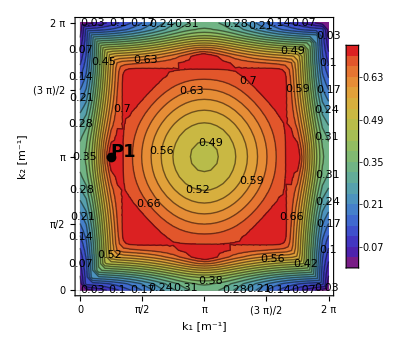
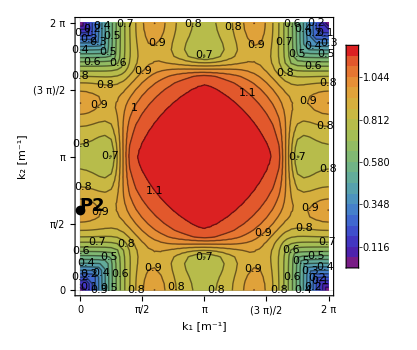
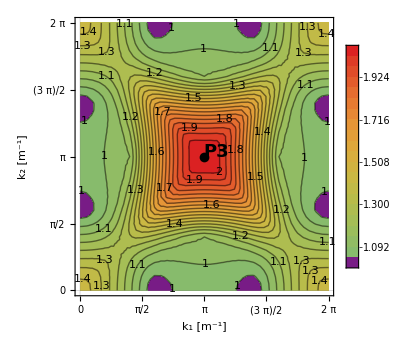
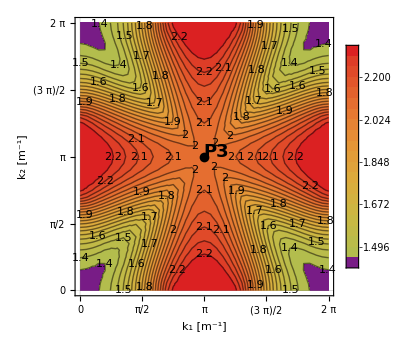

Contour plot relativi alle superfici sopra riportate. Sono rappresentati i punti di Dirac e i punti stazionari

Rappresentando, per le prime quattro superfici di dispersione, il dominio fino a 2π si può notare che in corrispondenza del punto k={π, (π})^T  il gradiente tende ad annullarsi definendo così una condizione di stazionarietà in cui la velocità di gruppo è nulla.

Dai contour plot si può dedurre l’evidente anisotropia del materiale presente in tutte le superfici; infatti, se il materiale fosse isotropo l’onda elastica si propagherebbe allo stesso modo nelle due direzioni (k_1 e k_2) formando così un disco. Questo non accade e lo si può notare già dalla seconda superficie di dispersione che vede delle forme distorte e lontane dall’essere delle circonferenze. Da notare invece la prima superficie di dispersione che presenta una serie di circonferenze centrate nel punto k = {π, π}^T che descrivono un comportamento isotropo localizzato; allontanandosi dal centro questo comportamento tende ad divergere verso forme più distorte.

I punti rappresentati nei primi due contour plot rappresentano i punti di Dirac, cioè quei punti angolosi in cui due superfici di dispersione si toccano; nell’intorno del punto la superficie di dispersione tende ad avere una forma conica (cono di Dirac) in cui il gradiente della superficie è costante. 
Nell’intorno del punto P3 si nota una condizione di stazionarietà in cui le superfici 3 e 4 sono tra loro tangenti. La stazionarietà esclude la presenza di punti di Dirac.

"Posizione e valore dei punti critici rappresentati sulle superfici di dispersione"
 | "Point" | "k_1L_1[-]" | "k_2L_1[-]" | "ω/ω_ref[-]" | "Dispersion surface"
"" | "P_1" | π/4 | π | 0.743 | "I-II"
"" | "P_2" | 0 | 3/5 π | 0.991 | "II-III"
"" | "P_3" | π | π | 2.086 | "III-IV"

I modi di vibrare riferiti ai punti in tabella sono rappresentati nelle figure dell’apposito capitolo.

### Influenza della snellezza

Come introdotto precedentemente sono state considerate - oltre alla snellezza iniziale λ=20 - altre due snellezze (una inferiore pari a 10 e una superiore pari a 50) per valutare l’effetto che queste hanno sulla propagazione dell’onda elastica nel metamateriale. I risultati sono sintetizzati nelle figure sottostanti.

```mathematica
{{-Graphics3D-, -Graphics3D-, -Graphics3D-}}
```

Rappresentazione delle prime sei superfici di dispersione al variare di λ

```mathematica
-Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D-
```

Confronto tra le singole superfici di dispersione al variare della snellezza λ

Dalle immagini si può notare come all’aumentare della snellezza le superfici di dispersione tendano a “schiacciarsi” verso il basso, riducendo la frequenza di oscillazione. Al contrario, riducendo la snellezza, le superfici tendono ad espandersi verso l’alto modificando altresì la loro forma.
Rimane invariata la linearità a basse frequenze delle prime due superfici di dispersione, mentre si notato variazioni molto importanti ad alte frequenze (dalla superficie 3 in poi).

### Influenza della parte immaginaria delle frequenze proprie

-Graphics3D-	-Graphics3D--Graphics3D-
Prime tre superfici di dispersione relative alla parte immaginaria dell’autovalore ω

Sono qui riportate le prime tre superfici derivanti dalla parte immaginaria che compone le frequenze angolari proprie calcolate precedentemente; analizzandole si possono notare le seguenti caratteristiche:

il basso ordine di grandezza delle frequenze;

la grande variabilità rispetto al loro valore medio;

la forte presenza di discontinuità

A fronte di queste considerazioni si può assumere che le frequenze proprie - soluzione del problema agli autovalori - siano da considerarsi puramente reali, data la scarsa rilevanza della parte immaginaria nel problema in studio, e che queste ultime derivino probabilmente dall’errore di calcolo del modello agli elementi finiti.

## Modi di vibrare

### Deformazioni nelle configurazioni P_1, P_2, P_3

```mathematica
-Graphics--Graphics--Graphics-
```

Spostamenti riferiti alle condizioni riportate nella tabella sopra (spostamenti in metri amplificati di un fattore 2 · 10^18)

Gli spostamenti sono stati ricavati studiano la risposta nel dominio delle frequenze della cella unitaria eccitata con le frequenze in tabella. Ne risultano gli spostamenti in figura; gli spostamenti generati dalle condizioni in P_1 risultano di un ordine di grandezza minori di quelli generati dalle altre configurazione, perciò si possono considerare trascurabili e si può affermare che la prima configurazione non genera evidenti deformazioni. D’altro canto, nelle due configurazioni successive si possono notare deformazioni riconducibili alla flessione nel piano per entrambi gli elementi; se in P_2 l’asta orizzontale è soggetta a effetti flessionali minori rispetto a quella verticale, in P_3 si può notare che entrambe le travi sono inflesse con una deformazione riconducibile al terzo modo di vibrare del modello shear type (incastro-pattino).

### Modi di vibrare del reticolo

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

Primi sei modi di vibrare del reticolo di travi per {k_1, k_2}^T = {π, π}^T (fattore di amplificazione: 1 · 10^5). I primi quattro modi generano effetti flessionali in tutte le travi, mentre gli ultimi due modi (5 e 6) mostrano un comportamento riconducibile a vibrazioni assiali

## Confronto delle mesh

### Elementi di teoria4

Per convergenza della soluzione approssimata agli EF verso la soluzione esatta del modello continuo si intende una convergenza in termini di energia (EPT) che avviene quando il numero di gradi di libertà del modello approssimato aumenta fino a tendere all’infinito (modello continuo). L’aumento di gradi di libertà può avvenire:

aumentando il numero di elementi finiti, infittendo la mesh: questo metodo è anche detto raffinamento di tipo h;

aumentando il grado del polinomio interpolante all’interno del EF (raffinamento di tipo p);

aumentando sia il numero di EF che il grado del polinomio interpolante, o raffinamento hp.

Ai fini di garantire una convergenza della soluzione approssimata verso la soluzione esatta del modello continuo, la modellazione del campo di spostamenti all'interno dell'elemento finito deve soddisfare i seguenti requisiti:

consistenza: questo requisito raggruppa i requisiti di completezza e compatibilità. Sia m l’indice variazionale, cioè l’ordine massimo di derivazione della EPT (Π(u) = U(u) - W(u), con U energia di deformazione elastica e W lavoro dei carichi esterni), allora devono essere garantiti i seguenti criteri:

completezza: le funzioni di forma devono essere tali da garantire la rappresentazione di moti rigidi (con energia di deformazione nulla) e stati a deformazione costante (per EF di dimensioni molto piccole). Questo implica che le funzioni di forma debbano riprodurre, su tutto il dominio Ω, polinomi di grado minore o uguale a m nelle coordinate globali;

compatibilità: la soluzione rappresentata dal campo di spostamento deve essere almeno di classe C^m all’interno del dominio (EF a energia finita) del EF e almeno C^(m-1) all’interfaccia del EF (EF conforme).

stabilità: garantita dalla definizione positiva dello jacobiano della trasformazione geometrica e dalla sufficienza del rango della matrice di rigidezza del singolo EF.

### Applicazione al modello 2D

Per l’analisi della convergenze è stato analizzato il nodo sulla superficie sorgente orizzonatale (come mostrato in figura); sono state confrontate sia le frequenze angolari adimensionali proprie sia lo spostamento del nodo normalizzato rispetto alla lunghezza L_1, per k_={π, π}^T con snellezza adimensionale λ = 20.

-Graphics--Graphics-
A sinistra: nodo di riferimento per la verifica della convergenza. A destra: tipi di EF 2D presenti in COMSOL Multiphysics®

S0no stati eseguiti i seguenti confronti:

primo raffinamento di tipo h: confronto tra mesh triangolare iniziale e primo infittimento (1088 elementi);

secondo raffinamento di tipo h: confronto tra primo e secondo infittimento della mesh (3729 elementi);

confronto tra elementi triangolari e quadrangolari (serendipity) con mesh inziale (dimensione elementi ∈ [0.002, 0.12]m);

raffinamento di tipo p: confronto tra elementi quadrangolari di tipo serendipity e di tipo lagrangiano (36 EF di dimensione ∈ [0.002, 0.12]m);

Per l’infittimento si è usato l’opzione di COMSOL Multiphysics® di adattamento automatico della mesh dove l’errore calcolato risulta alto; il modello viene quindi nuovamente risolto con la mesh rifinita. Sono stati eseguiti due infittimenti rispetto alla mesh di partenza.

### Differenza su ω - primo e secondo raffinamento di tipo h

"Confronto tra mesh iniziale e primo infittimento (ω/ω_ref)"
 | "Mode" | "FEM Mesh 0" | "FEM Mesh Adapt 1" | "Difference [%]"
"" | 1 | 0.480085 | 0.480003 | 0.017
"" | 2 | 1.21482 | 1.20664 | 0.673509
"" | 3 | 2.07407 | 2.07004 | 0.194251
"" | 4 | 2.07412 | 2.07011 | 0.193286
"" | 5 | 3.19071 | 3.1871 | 0.113136
"" | 6 | 3.26692 | 3.25917 | 0.237367		"Confronto tra primo e secondo infittimento (ω/ω_ref)"
 | "Mode" | "FEM Mesh Adapt 1" | "FEM Mesh Adapt 2" | "Difference [%]"
"" | 1 | 0.480003 | 0.479979 | 0.00503196
"" | 2 | 1.20664 | 1.2021 | 0.376415
"" | 3 | 2.07004 | 2.06794 | 0.101856
"" | 4 | 2.07011 | 2.06799 | 0.102779
"" | 5 | 3.1871 | 3.18595 | 0.0360735
"" | 6 | 3.25917 | 3.25473 | 0.136122

Dalle tabelle sopra riportate si può notare come la differenza percentuale tra i valori dei parametri scelti è molto basso (un ordine di grandezza inferiore rispetto al parametro) già con il primo confronto (mesh coarse e primo infittimento). L’ulteriore infittimento non crea sostanziali differenze nel calcolo delle frequenze angolari proprie; si può perciò affermare che la mesh iniziale - con EF triangolari a 6 nodi e funzioni di forma quadratiche - fornisce dei risultati sufficientemente accurati senza richiedere grandi capacità computazionali. È quindi possibile utilizzare la mesh iniziale per calcolare le frequenze proprie.

### Differenza su u - primo e secondo raffinamento di tipo h

"Confronto tra mesh iniziale e primo infittimento (u/L_1)"
 | "Mode" | "FEM Mesh 0" | "FEM Mesh Adapt 1" | "Difference [%]"
"" | 1 | 1.41×10^-6 | 1.41×10^-6 | 0
"" | 2 | 1.40992×10^-6 | 1.40999×10^-6 | -0.00499149
"" | 3 | 6.64279×10^-7 | 6.63961×10^-7 | 0.0479306
"" | 4 | 1.0028×10^-7 | 6.48243×10^-7 | -546.431
"" | 5 | 1.40679×10^-6 | 1.40962×10^-6 | -0.200899
"" | 6 | 1.40881×10^-6 | 1.40963×10^-6 | -0.0581275		"Confronto tra primo e secondo infittimento (u/L_1)"
 | "Mode" | "FEM Mesh Adapt 1" | "FEM Mesh Adapt 2" | "Difference [%]"
"" | 1 | 1.41×10^-6 | 1.41×10^-6 | 0
"" | 2 | 1.40999×10^-6 | 1.41×10^-6 | -0.000876289
"" | 3 | 6.63961×10^-7 | 6.63286×10^-7 | 0.101664
"" | 4 | 6.48243×10^-7 | 6.63857×10^-7 | -2.40876
"" | 5 | 1.40962×10^-6 | 1.41×10^-6 | -0.0268826
"" | 6 | 1.40963×10^-6 | 1.40995×10^-6 | -0.0225719

Questione diversa se si analizza lo spostamento del nodo precedentemente indicato; in particolare per il quarto modo di vibrare si può notare un errore molto elevato riferito al primo infittimento che si riduce a circa il 2% durante il secondo confronto. Concentrandosi sul secondo infittimento, le differenze riferite ai modi 3 e 4 risultano essere almeno un ordine di grandezza superiore alle altre. Ne consegue che - per quanto riguarda lo spostamento del nodo in esame - la convergenza non è garantita fino al secondo infittimento e che ulteriori raffinamenti dovrebbero essere eseguiti perché si veda una stabilizzazione del valore in esame.

### Differenza tra mesh triangolare e quadrangolare

"Confronto tra mesh triangolare e quadrangolare serendipity (ω/ω_ref)"
 | "Mode" | "FEM Triangular" | "FEM Quadrilateral" | "Difference [%]"
"" | 1 | 0.480085 | 0.480523 | -0.0913029
"" | 2 | 1.21482 | 1.24765 | -2.70241
"" | 3 | 2.07407 | 2.09026 | -0.780523
"" | 4 | 2.07412 | 2.09026 | -0.778113
"" | 5 | 3.19071 | 3.19965 | -0.280476
"" | 6 | 3.26692 | 3.2903 | -0.715573	"Confronto tra mesh triangolare e quadrangolare serendipity (u/_L_1)"
 | "Mode" | "FEM Triangular" | "FEM Quadrilateral" | "Difference [%]"
"" | 1 | 1.41×10^-6 | 1.41×10^-6 | 0
"" | 2 | 1.40992×10^-6 | 1.41×10^-6 | -0.00586761
"" | 3 | 6.64279×10^-7 | 1.24276×10^-9 | 99.8129
"" | 4 | 1.0028×10^-7 | 6.64683×10^-7 | -562.826
"" | 5 | 1.40679×10^-6 | 1.40989×10^-6 | -0.220141
"" | 6 | 1.40881×10^-6 | 1.40968×10^-6 | -0.0613371

Come analizzato precedentemente la differenze tra le due tipologie di EF non si rispecchia nel calcolo delle frequenze, cosa che invece accade se si guarda lo spostamento del nodo. Anche in questo caso i modi interessati dal grande errore sono il terzo e il quarto. 
Si può quindi affermare la possibile presenza di un errore elevato nel calcolo dello spostamento per quanto riguarda la mesh triangolare che non risulta sufficientemente accurata.

### Differenza tra EF serendipity e di Lagrange

Un elemento quadrangolare di tipo serendipity si differenzia da quello di tipo lagrangiano dalla mancanza del nodo interno centrale. Entrambi sono rappresentati da funzioni di forma biquadratiche e questo implica un minor numero di gradi di libertà totali che corrispondono a un’accuratezza molto simile all’elemento finito di Lagrange. Come riportato da Felippa (2004)5 l’elemento serendipity è stato pesantemente usato a partire dagli anni ‘70 del ‘900 grazie alla minore capacità computazionale richiesta, ma con la sempre maggior potenza dei calcolatori moderni questo elemento è stato sostituito da quello a nove nodi in particolar modo per problemi dinamici.

In COMSOL Multiphysics® l’elemento di default è quello di tipo serendipity; è stato quindi effettuato un confronto tra le due tipologie di elemento finito per valutare, se possibile, il più adatto al problema in esame. Il confronto è stato effettuato sulla mesh iniziale (coarse) con elementi quadrangolari biquadratici, in quanto - applicando elementi lagrangiani su mesh più raffinate - il numero di gradi di libertà era tale da saturare la memoria del calcolatore in possesso. Di seguito sono riportate i risultati su ω e su u:

"Confronto tra EF quadrangolare serendipity e di Lagrange (ω/ω_ref)"
 | "Mode" | "EF serendipity" | "EF Lagrange" | "Difference [%]"
"" | 1 | 0.480523 | 0.480389 | 0.0279548
"" | 2 | 1.24765 | 1.2315 | 1.29486
"" | 3 | 2.09026 | 2.08248 | 0.372181
"" | 4 | 2.09026 | 2.08248 | 0.372181
"" | 5 | 3.19965 | 3.19775 | 0.0596587
"" | 6 | 3.2903 | 3.2782 | 0.367715	"Confronto tra EF quadrangolare serendipity e di Lagrange (u/_L_1)"
 | "Mode" | "EF serendipity" | "EF Lagrange" | "Difference [%]"
"" | 1 | 1.41×10^-6 | 1.41×10^-6 | 0
"" | 2 | 1.41×10^-6 | 1.41×10^-6 | 0
"" | 3 | 1.24276×10^-9 | 7.53403×10^-10 | 39.3765
"" | 4 | 6.64683×10^-7 | 6.65628×10^-7 | -0.142151
"" | 5 | 1.40989×10^-6 | 1.40999×10^-6 | -0.0070757
"" | 6 | 1.40968×10^-6 | 1.41×10^-6 | -0.0227983

La differenza dei risultati ottenuti si può considerare trascurabile in entrambi i casi, a meno di un’anomalia sul modo 2 (sul calcolo di ω) e sul modo 3 (sul calcolo di u).

### Convergenza della mesh per il modello 1D

È stato eseguito un confronto tra varie mesh sul modello beam alla Eulero - Bernoulli. I risultati sono rappresentati nelle figure sotto.

```mathematica
-Graphics3D--Graphics3D-
-Graphics3D--Graphics3D-
-Graphics3D--Graphics3D-
```

Comparazione delle superfici di dispersione all’infittimento della mesh nel modello di trave - λ=20

Si nota come a basse frequenza (e lunghezze d’onda grandi) anche la mesh più grossolana riesce a rappresentare sufficientemente bene la propagazione dell’onda e quindi le superfici di dispersione correlate. Al contrario ad alte frequenze - che corrispondono a lunghezze d’onda piccole - la mesh coarse evidenzia degli errori (come rappresentato nella sesta superficie di dispersione) e varianze maggiori rispetto alle mesh più fitte.

-Graphics3D-

Zoom della sesta superficie di dispersione - λ=20

Differenza percentuale tra mesh del modello beam EB per {k_1,k_2}={π,π} (ω/ω_ref)
 | Mode | Coarse-Fine [%] | Fine-Extra Fine [%]
 | 1 | 0.000719137 | -0.0000456753
 | 2 | 0.00520941 | -0.00175143
 | 3 | 0.0392553 | 0.0124789
 | 4 | 0.0392553 | 0.0124789
 | 5 | 0.295682 | 0.0982624
 | 6 | 19.455 | 0.0982624

La tabella sopra mostra la differenza percentuale dei valori di ω/ω_ref per vettore d’onda k = {π, (π})^T. Si nota come le differenze tendano ad aumentare all’aumentare della frequenza di oscillazione (e quindi del modo di vibrare). Differenze significative sono evidenti negli ultimi due modi passando da una mesh grossolana a una più fine; infittendo ulteriormente la mesh la differenza si riduce fino a ordini di grandezza trascurabili.

## Convergenza della soluzione

Come descritto nel capitolo precedente si ha convergenza dei risultati quando la soluzione approssimata agli elementi finiti tende alla soluzione esatta. Non essendo presente una soluzione analitica del problema è stata considerata - ai fini del confronto - una soluzione per il modello di trave derivante dalla letteratura scientifica6. In particolare i risultati sono stati confrontati con un modello di trave alla Eulero-Bernoulli che presenta un pattino a metà lunghezza, vincolato da una molla traslazionale; fissando la rigidezza della molla a un valore molto elevato si simula la continuità del taglio e si garantisce la corrispondenza con il modello 2D. Un ulteriore confronto è stato effettuato creando, a partire dal modello di trave precedente, una geometria composta da due elementi beam (uno orizzontale e uno verticale) connessi tra loro da una cerniera con molla rotazionale; anche in questo caso è stato sufficiente fissare la rigidezza della molla a un valore alto per definire il vincolo di incastro tra gli elementi. Confrontando i due modelli 1D non è stata notata alcuna differenza significativa né per quanto riguarda il comportamento della cella unitaria né per quanto riguarda le superfici di dispersione. Di seguito viene riportato il confronto tra le superfici di dispersione valutate per al variare della snellezza adimensionale λ.

### λ=10

```mathematica
-Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D-
```

Comparazione tra le superfici di dispersione del modello 2D e quelle dei modelli di trave - λ=10

A snellezze molto basse (ad esempio λ=10) il modello di trave non è in grado di rappresentare sufficientemente bene il comportamento dinamico del reticolo. Questo è dovuto principalmente al limite del modello di trave alle Eulero-Bernloulli, il quale ben approssima il comportamento di elementi snelli. Ulteriori analisi con modelli più sofisticati (ad esempio quello di Rayleigh che tiene conto dell’inerzia rotazionale dell’elemento) possono essere considerati per verificare la convergenza anche a snellezze basse.

#### Tabelle dei confronti - λ=10

La notazione 2D fa riferimento ai dati del modello bi-dimensionale, SG indica i dati derivanti dal modello sliding-grid, mentre EB fa riferimento al modello con molla rotazionale.

Media e deviazione standard della differenza tra le superfici di dispersione (ω/ω_ref)
 | Mode | Mean(2D-SG) | Std(2D-SG) | Mean(2D-EB) | Std(2D-EB)
 | 1 | 0.0602824 | 0.0585169 | 0.060252 | 0.0585025
 | 2 | 0.139297 | 0.0591247 | 0.139195 | 0.059042
 | 3 | 0.0711488 | 0.104659 | 0.0708725 | 0.1047
 | 4 | 0.0562785 | 0.0679231 | 0.0550933 | 0.0678527
 | 5 | -0.155165 | 0.305287 | -0.158589 | 0.305074
 | 6 | -0.114674 | 0.319617 | -0.120053 | 0.320937

Un ulteriore confronto è stato effettuato per k={π, π}^T e riportato di seguito.

Differenza percentuale del modello 2D con i modelli beam per {k_1,k_2}={π,π} (ω/ω_ref)
 | Mode | 2D-SG [%] | 2D-EB [%]
 | 1 | -6.39926 | -6.39931
 | 2 | 6.27195 | 6.27544
 | 3 | 12.574 | 12.5499
 | 4 | 12.574 | 12.55
 | 5 | 2.50562 | 2.39854
 | 6 | 6.55041 | 6.44777

### λ=20

Aumentando la snellezza ci si aspetta una migliore convergenza dei risultati e quindi una minor differenza tra le superfici di dispersione tra il modello bi-dimensionale e quelli monodimensionali.

```mathematica
-Graphics3D--Graphics3D-
-Graphics3D--Graphics3D-
-Graphics3D--Graphics3D-
```

Comparazione tra le superfici di dispersione del modello 2D e quelle dei modelli di trave - λ=20

#### Tabelle dei confronti - λ=20

Al netto dell’ultima superficie, si nota una buona similarità nei risultati. Un confronto quantitativo è riportato nella seguente tabella.

Media e deviazione standard della differenza tra le superfici di dispersione (ω/ω_ref)
 | Mode | Mean(2D-SG) | Std(2D-SG) | Mean(2D-EB) | Std(2D-EB)
 | 1 | 0.016688 | 0.0152438 | 0.0166767 | 0.0152413
 | 2 | 0.0530788 | 0.0239996 | 0.0530704 | 0.0240177
 | 3 | 0.0567303 | 0.0183264 | 0.0565921 | 0.0182561
 | 4 | 0.0485316 | 0.0493534 | 0.048055 | 0.0495102
 | 5 | -0.114139 | 0.0725342 | -0.115676 | 0.0723059
 | 6 | -0.103628 | 0.065247 | -0.10594 | 0.0648518

Un ulteriore confronto è stato effettuato per k={π, π}^T e riportato di seguito.

Differenza percentuale del modello 2D con i modelli beam per {k_1,k_2}={π,π} (ω/ω_ref)
 | Mode | 2D-SG [%] | 2D-EB [%]
 | 1 | -2.79023 | -2.79023
 | 2 | 7.91256 | 7.92079
 | 3 | 3.79315 | 3.76904
 | 4 | 3.79545 | 3.77134
 | 5 | 1.53587 | 1.42617
 | 6 | 3.83302 | 3.72589

Rispetto al caso precedente si nota che le differenze percentuali si siano ridotte di due terzi per i modi 3 e 4 e circa della metà per i modi 5 e 6. Si è notato, invece, un’aumento di un punto percentuale dell’errore nel secondo modo.

### λ=50

```mathematica
-Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D-
```

Comparazione tra le superfici di dispersione del modello 2D e quelle dei modelli di trave - λ=50

#### Tabelle dei confronti - λ=50

Differenza percentuale del modello 2D con i modelli beam per {k_1,k_2}={π,π} (ω/ω_ref)
 | Mode | 2D-SG [%] | 2D-EB [%]
 | 1 | -0.428721 | -0.428773
 | 2 | 6.45951 | 6.463
 | 3 | 3.96285 | 3.91403
 | 4 | 3.96746 | 3.91865
 | 5 | -3.62135 | -3.62567
 | 6 | 2.40596 | 2.40233

Con snellezza λ=50 si nota un’ulteriore diminuzione delle differenze per la superficie numero 6, mentre è evidente un’oscillazione dei valori negli altri modi di vibrare. In generale si può affermare la convergenza della soluzione dovuta al fatto che la variazione tende a ridursi all’aumentare della snellezza. Ci si può aspettare che, con snellezze ancora maggiori, le due soluzioni tendano a convergere ulteriormente.

## Conclusioni

A valle dei risultati ottenuti e tenendo conto della convergenza a documenti presenti in letteratura scientifica, si può sottoscrivere la bontà del modello bi-dimensionale agli elementi finiti nel descrivere i modi di propagazione di onde elastiche nel metamateriale considerato attraverso le condizioni al contorno di Floquet-Bloch.

È stata inoltre dimostrata la pesante anisotropia dovuta al fatto che l’onda elastica non si propaga allo stesso modo nel mezzo considerato, con l’unica eccezione della prima superficie di dispersione che presenta una zona di isotropia localizzata.

È stata confermata la dipendenza delle frequenze e quindi della relazione di dispersione dalla snellezza degli elementi, generando uno “schiacciamento” delle superfici all’aumentare della snellezza (e quindi all’aumentare della profondità fuori piano del reticolo) e un’espansione delle superfici al diminuire della snellezza -  con forme delle superfici pressoché simili a quelle di partenza (λ=20).

Si è dimostrata la bassa dipendenza dei risultati in termini di frequenze dalla mesh, in particolare da una mesh molto fitta, da cui i risultati con mesh più grossolane non si discostano significativamente. Inoltre, si è dimostrato non necessario adottare EF di tipo lagrangiano (EF quadrangolari a 9 nodi) rispetto a quelli di tipo serendipity a 8 nodi data la differenza trascurabile dei risultati in frequenza.

È stata dimostrata la convergenza delle soluzioni 2D alle soluzioni 1D all’aumentare della snellezza con errori percentuali che si riducono progressivamente all’aumentare di λ.

 Ulteriori analisi potrebbero essere effettuate variando la geometria del reticolo, in particolare considerando una cella unitaria rettangolare piuttosto che quadrata, analizzando così gli effetti della geometria sull’anisotropia del mezzo, oppure applicando dei prestress agli elementi per comprendere come variano le superfici di dispersione e quindi come si propagano le onde elastiche - come già fatto da Bordiga et al., 2019.

### References

1	G. Bordiga, L. Cabras, A. Piccolroaz, and D. Bigoni, "Prestress tuning of negative refraction and wave channeling from flexural sources", Appl. Phys. Lett. 114, 041901 (2019) https://doi.org/10.1063/1.5084258

2	G. Bordiga, L. Cabras, D. Bigoni, A. Piccolroaz, Free and forced wave propagation in a Rayleigh-beam grid: Flat bands, Dirac cones, and vibration localization vs isotropization, International Journal of Solids and Structures, Volume 161, 2019, Pages 64-81, ISSN 0020-7683, https://doi.org/10.1016/j.ijsolstr.2018.11.007. (https://www.sciencedirect.com/science/article/pii/S0020768318304384)

3	G. Bordiga, L. Cabras, A. Piccolroaz, D. Bigoni,Dynamics of prestressed elastic lattices: Homogenization, instabilities, and strain localization,
Journal of the Mechanics and Physics of Solids, Volume 146, 2021, 104198, ISSN 0022-5096, https://doi.org/10.1016/j.jmps.2020.104198

4	A. Piccolroaz, "Lezione 2: EF per piastre", Corso di Meccanica Computazionale delle Strutture 2, Università degli Studi di Trento (2021)

5	C. A. Felippa, "Introduction to finite element methods", Department of Aerospace Engineering Sciences and Center for Aerospace Structures, University of Colorado (2004)

6	G. Bordiga, D. Bigoni, A. Piccolroaz, "Tensile material instabilities in elastic beam lattices llead to a closed stability domain", Philosophical Transactions A (2021)

8	Phani, Woodhouse, and Fleck, “Wave Propagation in Two-Dimensional Periodic Lattices.”, Department of Engineering, Cambridge University